## Derivation of R0 bound

```mathematica
twodlineresultsfig = Plot[(9)/(4.5)*x*UnitStep[2-x],{x,-2,2},PlotRange->{{-5,5},All},ColorFunction->Function[{x,y},ColorData["LakeColors"][Exp[-y]]],Axes->False];
xaxisresultsfig = Graphics[{Thin,Black,Line[{{-5,0},{5,0}}]}];
x1axisresultsfig = Graphics[{Thick,Blue,Dotted,Line[{{-5,2.5},{5, -2.5}}]}];
yaxisresultsfig = Graphics[{Thin,Black,Line[{{0,-5},{0,5}}]}];
endpointresultsfig=Graphics[{Red,Disk[{2,4},.1]}];
verticalnbdevery = Graphics[{Cyan,Rectangle[{2,5},{1,-5}]}];
horizontalnbdevery=Graphics[{Yellow,Opacity[0.8],Rectangle[{5,3},{-5,4}]}];
horizontalangle =  Graphics[Style[Text["θ_1",{0.7,.4}],FontSize->24]];
verticalangle = Graphics[Style[Text["θ_2",{0.4,2}],FontSize->24]];
horizontalbeta=Graphics[Style[Text["β",{-5.5,3.5}],FontSize->24]];
verticalbeta=Graphics[Style[Text["β",{1.5,5.5}],FontSize->24]];
everyderivation1=Show[verticalnbdevery,horizontalnbdevery,xaxisresultsfig,twodlineresultsfig,x1axisresultsfig,yaxisresultsfig,endpointresultsfig,horizontalangle,verticalangle,horizontalbeta,verticalbeta,
Graphics[Style[Text["(A)",{-5.5,5.5}],FontSize->24]]];
```

```mathematica
twodlineresultsfig2 =Plot[(4.5)/(9)*x*UnitStep[4-x],{x,-4,4},PlotRange->{{-5,5},All},ColorFunction->Function[{x,y},ColorData["LakeColors"][Exp[-y]]],Axes->False];
(* Graphics[Line[{{-5,-2.5},{4,2}}]];*)
xaxisresultsfig2 = Graphics[{Thin,Black,Line[{{-5,0},{5,0}}]}];
x1axisresultsfig2 = Graphics[{Thick,Blue,Dotted,Line[{{-2.5,5},{2.5, -5}}]}];
yaxisresultsfig2 = Graphics[{Thin,Black,Line[{{0,-5},{0,5}}]}];
endpointresultsfig2=Graphics[{Red,Disk[{4,2},.1]}];
horizontalnbdevery2 = Graphics[{Yellow,Opacity[0.8],Rectangle[{-5,2},{5,1}]}];
verticalnbdevery2 = Graphics[{Cyan,Rectangle[{3,-5},{4,5}]}];
horizontalangle2 =  Graphics[Style[Text["θ_1",{2,.5}],FontSize->24]];
verticalangle2 = Graphics[Style[Text["θ_2",{0.5,1}],FontSize->24]];
horizontalbeta2=Graphics[Style[Text["β",{-5.5,1.5}],FontSize->24]];
verticalbeta2=Graphics[Style[Text["β",{3.5,5.5}],FontSize->24]];
everyderivation2=Show[verticalnbdevery2,horizontalnbdevery2,xaxisresultsfig2,x1axisresultsfig2,yaxisresultsfig2, endpointresultsfig2,twodlineresultsfig2,horizontalangle2,verticalangle2,horizontalbeta2,verticalbeta2, 
Graphics[Style[Text["(B)",{-5.5,5.5}],FontSize->24]]];
```

```mathematica
nbdanyresults=Graphics[{Green,Rectangle[{1,4},{2,3}]}];
horizontalbetaany=Graphics[Style[Text["β",{1.5,4.4}],FontSize->24]];
verticalbetaany=Graphics[Style[Text["β",{2.4,3.6}],FontSize->24]];
anyderivation1=Show[nbdanyresults,xaxisresultsfig,x1axisresultsfig,yaxisresultsfig,endpointresultsfig,twodlineresultsfig,horizontalangle,verticalangle,horizontalbetaany,verticalbetaany,
Graphics[Style[Text["(C)",{-5.5,5.5}],FontSize->24]]];
```

```mathematica
nbdanyresults2=Graphics[{Green,Rectangle[{3,1},{4,2}]}];
horizontalbetaany2=Graphics[Style[Text["β",{3.5,2.5}],FontSize->24]];
verticalbetaany2=Graphics[Style[Text["β",{4.4,1.6}],FontSize->24]];
anyderivation2=Show[nbdanyresults2,endpointresultsfig2,twodlineresultsfig2,xaxisresultsfig2,x1axisresultsfig2,yaxisresultsfig2,horizontalangle2,verticalangle2,horizontalbetaany2,verticalbetaany2,Graphics[Style[Text["(D)",{-5.5,5.5}],FontSize->24]]];
```

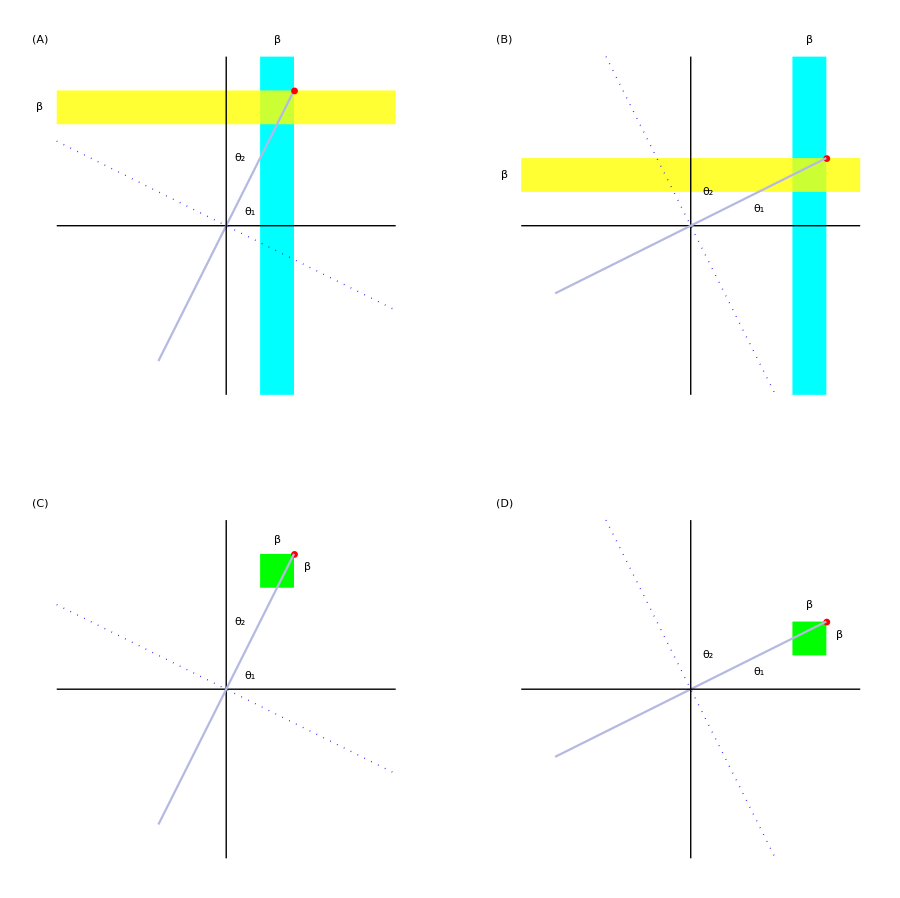

```mathematica
picturelegend=LineLegend[{Red,Blue,Directive[Thick,Dotted,Blue],Directive[Thin,Black]},{"infections","memories","x_2 axis","epitope-aligned axes"},LabelStyle->{FontSize->24,Black}];
derivationplots =Legended[ GraphicsGrid[{{everyderivation1,everyderivation2},{anyderivation1,anyderivation2}}],picturelegend];
Show[derivationplots,ImageSize->900]
```